```mathematica
dateMouseSessionListV1={{"071820","Mouse21019","Session1"},{"080820","Mouse21019","Session2"},{"081120","Mouse21019","Session1"},{"082520","Mouse21020","Session3"},{"072520","Mouse21036","Session2"},{"080920","Mouse21036","Session1"},{"081120","Mouse21036","Session1"},{"081320","Mouse21036","Session2"},{"071920","Mouse21062","Session2"},{"080620","Mouse21062","Session1"},{"091320","Mouse21068","Session1"},{"092720","Mouse21068","Session1"},{"092920","Mouse21068","Session1"},{"091620","Mouse23336","Session1"},{"092220","Mouse23336","Session1"},{"111220","Mouse23385","Session2"},{"111820","Mouse23385","Session1"},{"121420","Mouse23312","Session2"},{"010621","Mouse23332","Session1"},{"010821","Mouse23332","Session2"},{"011321","Mouse23332","Session1"},{"011821","Mouse23332","Session1"},{"010921","Mouse23305","Session2"},{"011121","Mouse23305","Session2"},{"030821","Mouse23321","Session1"},{"031121","Mouse23321","Session2"},{"031621","Mouse23321","Session2"},{"031921","Mouse23321","Session2"},{"030721","Mouse23324","Session2"},{"031621","Mouse23324","Session2"}};
```

```mathematica
dateMouseSessionListV2m={{"090320","Mouse21011","Session3"},{"090820","Mouse21011","Session2"},{"092620","Mouse21011","Session1"},{"091520","Mouse21069","Session2"},{"090320","Mouse21076","Session2"},{"090520","Mouse21076","Session1"},{"112020","Mouse23383","Session2"},{"112120","Mouse23383","Session2"},{"112220","Mouse23386","Session1"},{"120520","Mouse23383","Session2"},{"010121","Mouse23382","Session1"},{"011521","Mouse23390","Session2"},{"011821","Mouse23390","Session2"},{"021221","Mouse23359","Session2"},{"021821","Mouse23310","Session1"},{"030221","Mouse23310","Session1"},{"031121","Mouse23310","Session1"},{"021721","Mouse23338","Session1"},{"022621","Mouse23338","Session1"},{"030221","Mouse23338","Session1"},{"031521","Mouse23338","Session2"},{"031921","Mouse23338","Session1"},{"072421","Mouse21151","Session2"},{"080121","Mouse22481","Session1"},{"072521","Mouse21133","Session1"},{"072121","Mouse21170","Session1"}};
```

```mathematica
(***Preferred spatial frequency***)
```

```mathematica
prefSFsV1=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/prefSFs_V1.txt","List"]];
```

```mathematica
prefSFsV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/prefSFs_V2m.txt","List"]];
```

```mathematica
v1Charts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsV1]}],prefSFsV1],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},Axes->False],BoxWhiskerChart[prefSFsV1,{{"Whiskers", Directive[Blue,Thick]}, {"Fences", Directive[Blue,Thick]},{"MedianMarker", Directive[Blue,Thickness[0.009]]}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsV1,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsV2m]}],prefSFsV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},Axes->False],BoxWhiskerChart[prefSFsV2m,{{"Whiskers", Directive[Purple,Thick]}, {"Fences", Directive[Purple,Thick]},{"MedianMarker", Directive[Purple,Thickness[0.009]]}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSFsV2m]}],prefSFsV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0.01,0.33}},FrameTicks->{{LinTicks[0.01,0.34,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],BoxWhiskerChart[prefSFsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},ChartStyle->Transparent,Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSFsV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False,ScalingFunctions->"Log"]];
```

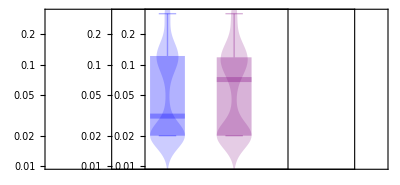

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```

```mathematica
(***Preferred speed***)
```

```mathematica
prefSpeedsV1=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V1/ValuesForPlotting/prefSpeeds_V1.txt","List"]];
```

```mathematica
prefSpeedsV2m=Flatten[ToExpression/@Import["F:/FigureGeneration/FigureS2/FigureS2Data/CellBodies/V2m/ValuesForPlotting/prefSpeeds_V2m.txt","List"]];
```

```mathematica
v1Charts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsV1]}],prefSpeedsV1],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsV1,{{"Whiskers", Directive[Blue,Thick]}, {"Fences", Directive[Blue,Thick]},{"MedianMarker", Directive[Blue,Thickness[0.009]]}},ChartStyle->Directive[Blue,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsV1,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Blue],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
pmCharts=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsV2m]}],prefSpeedsV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsV2m,{{"Whiskers", Directive[Purple,Thick]}, {"Fences", Directive[Purple,Thick]},{"MedianMarker", Directive[Purple,Thickness[0.009]]}},ChartStyle->Directive[Purple,Opacity[0.3]],Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Purple],Frame->False,ScalingFunctions->"Log"],FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[ListLogPlot[Partition[Riffle[Table[RandomReal[{0.55,0.85}],{Length[prefSpeedsV2m]}],prefSpeedsV2m],2],PlotStyle->Transparent,PlotMarkers->Graphics[{Transparent,Circle[]},ImageSize->5.5],PlotRange->{{-0.63,2},{0,1500}},FrameTicks->{{LinTicks[0,1500,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]],ListLogPlot[Partition[Partition[Riffle[Table[-0.6,{Length[Range[5,720,55]]}],Range[5,720,55]],2],1],PlotStyle->Black,PlotRange->{{-0.63,2},{0,1500}},Axes->False],BoxWhiskerChart[prefSpeedsV2m,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},ChartStyle->Transparent,Frame->False,ScalingFunctions->"Log"],DistributionChart[prefSpeedsV2m,ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False,ScalingFunctions->"Log"]];
```

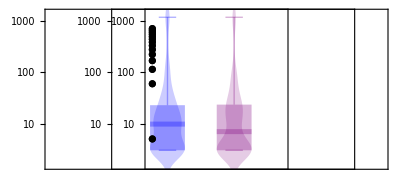

```mathematica
GraphicsRow[{v1Charts,pmCharts,transp},Spacings->{{-280,-280,-320}}]
```